Initialization cell: initializes plot font and colour options so as to not require calling them every time a plot is made.

```mathematica
Needs["HierarchicalClustering`"]
SetOptions[Plot,ImageSize->Medium,PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[MatrixPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[Plot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black}];
SetOptions[ParametricPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->19}];
SetOptions[ListPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black},PlotMarkers->None,Filling->Axis];
```

Pitchfork bifurcation example: It is known as Pitchfork per Strogatz whilst as Saddlenode bifurcation per Roberto Munez Alicea.  Surprisingly, the terminology varies between textbooks.  The prize for naming this goes to Abraham and Shaw (1988) for calling it blue sky bifurcation.

{{x→0},{x→-√μ},{x→√μ}}

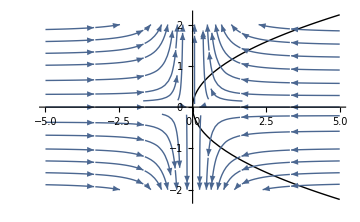

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
Solve[xdot==0,x]
μ=0;
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-5,5},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,y},{x,-5,5},{y,-2,2},GridLines->Automatic,StreamScale->Medium]
]
```

For the non linear evolution equation that governs liquid film dynamics, the derivative of the growth rate equation resembles f(x,μ)=μ x - x^3.  For the liquid film, μ=(2 Pm/(1+Bi)^2 - 2 Pm)/Sn.  This demonstrates, what is known as, supercritical pitchfork bifurcation.  The non-linear (cubic term) has a stabilizing effect (it is the surface tension term) while the value of μ lends stability (μ<0), weak stability (μ=0) and instability (μ>0).  Physically, this can be related to the fact when μ<0, the Permeability term overwhelms thermocapillary instability; μ=0, there is a balance struck between porosity and thermocapillarity or the surface tension term is large enough to reduce μ≈0.  When μ>0, the thermocapillary term has the ability to overwhelm stabilizing porosity.

```mathematica
μ=((2 Pm)/(Bi+1)^2-2 Pm)/Sn
```

{x→0,x→-√μ,x→√μ}

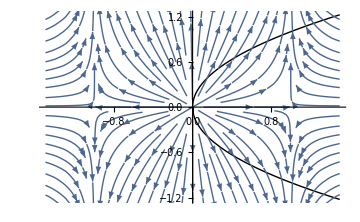

```mathematica
Clear[x,xdot,μ,y];
xdot=μ x-(x)^3;
roots=Solve[xdot==0,x]//Flatten
μ=1;
μmax=If[μ≠ 0,1.5Abs[μ],3];
Plot[{μ x-x^2},{x,-1,1}];
Show[Plot[{Sqrt[μ],-Sqrt[μ]},{μ,-μmax,μmax},PlotStyle->{{Thick,Black},{Thick,Black}}],
StreamPlot[{μ x-x^3,y},{x,-μmax,μmax},{y,-μmax,μmax},GridLines->Automatic,StreamScale->Medium]
]
```

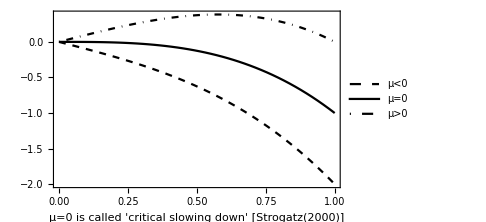

```mathematica
Plot[{-x-x^3,-x^3,x-x^3},{x,0,1},PlotLegends->{"μ<0","μ=0","μ>0"},PlotStyle->{{Dashed,Thick,Black},{Thick,Black},{DotDashed,Thick,Black}},AxesLabel->{"x","f(x,μ)"},Frame->True,FrameLabel->"μ=0 is called 'critical slowing down' [Strogatz(2000)]"]
```